#### 1. Summary

This document is an exhibition of plotting the so called pdf files (In DISCUS). The data will be imported and plotted in this module

```mathematica
Import[NotebookDirectory[]<>"zrsets.mac"]
```

read             
cell p.cll,10,10,10
#                
pdf              
  set rang,10,0.02
  set qsig,0.0     
  set rad,neutron    
#                
  set qmax,0.0  
  set therm,off 
  calc             
  save pdf,pattern1.pdf      
#            
  set qmax,20.0
  set therm,off
  calc         
  save pdf,pattern2.pdf  
#                   
  set qmax,0.0        
  set therm,gauss     
  calc                
  save pdf,pattern3.pdf
#
  set qmax,20.0        
  set therm,gauss     
  calc                
  save pdf,pattern4.pdf
exit

#### 2. Code

```mathematica
SetDirectory["C:\\Users\\sghwan28\\"];

pdfdata[file_]:=Module[{localFileName,filename,oridata,newdata,output},(
filename=ToString[file];
localFileName=FileNameJoin[{Directory[],filename}];

If[FileExistsQ[localFileName]==True,
oridata=SemanticImport[filename];
oridata=Drop[oridata,None,{3,4}]//Normal;
output=ListLinePlot[oridata,PlotRange->All,PlotLabel->StringDelete[filename,".pdf"]],

Print[Row[{"The Document '",filename,"' does not exist"}]]])]


(* or use this code to get the orginal dataset for plotting *)
pdfdata2[file_]:=Module[{localFileName,filename,oridata,newdata,output},(
filename=ToString[file];
localFileName=FileNameJoin[{Directory[],filename}];

If[FileExistsQ[localFileName]==True,
oridata=SemanticImport[filename];
oridata=Drop[oridata,None,{3,4}],

Print[Row[{"The Document '",filename,"' does not exist"}]]])]
```

#### 3. use case

```mathematica
pdfdata[happy]
```

The Document 'happy' does not exist

The argument of pdfdata should be a proper file name with .pdf extension.

```mathematica
pattern1=pdfdata["pattern1.pdf"];
pattern2=pdfdata["pattern2.pdf"];
pattern3=pdfdata["pattern3.pdf"];
pattern4=pdfdata["pattern4.pdf"];
```

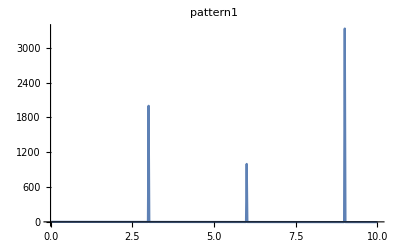
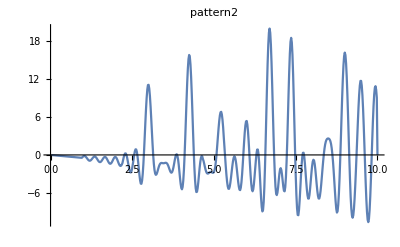
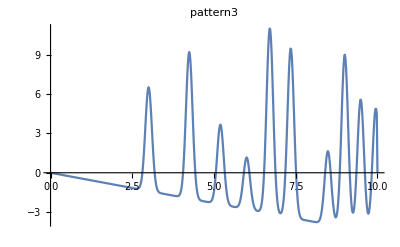
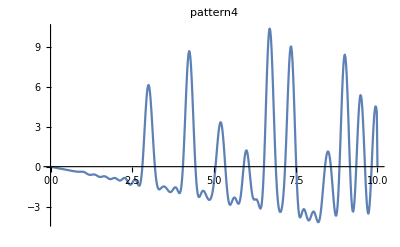

```mathematica
{pattern1,pattern2,pattern3,pattern4}
```

```mathematica
pdfdata2["pattern1.pdf"]
```

Dataset[<>]